# Patent Claims Analytics

American patent documents are well-structured documents, with clear intentions and conclusions to be referenced as valuable precedents. These structured elements of patents make them a perfect candidate for applying NLP to retrieve, extract, and recognize information. Here, Wolfram’s natural language processing framework will allow us to identify the most frequently used words in patent claims and cluster patents that claim similar subject matter based on vector representations of words using a neural network model called GloVe.

## Importing Patent Grant Full Text (without Images) from USPTO

Patent grant full text (without images) from USPTO Bulk Data are downloaded as zip files and extracted into xml files.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\WSS\Project

```mathematica
allLinks = Import["https://bulkdata.uspto.gov/","Hyperlinks"];
fulltextLinks = Flatten[StringCases[allLinks,"https://bulkdata.uspto.gov/data2/patent/grant/redbook/fulltext"~~__]];
zipLinks = Association[Rule[FileBaseName[#],Flatten[StringCases[Import[#,"Hyperlinks"],__~~"zip"]]]&/@fulltextLinks];
```

```mathematica
zipFiles=Map[URLDownload[#,Last[FileNameSplit[#]]]&,Take[zipLinks[["2008"]],All]];
xmlFiles = First@*ExtractArchive /@ zipFiles;
```

## Parsing and Reading Patents

Each patent is parsed by separating with headings of xml files and parsed. For each patent, patent information including the patent number, title, number of claims, and claim text is extracted.

```mathematica
parseAllPatent[files_] :=
	Module[
		{patentsStream, patent},
		patentsStream = OpenRead[files];
		patent = Find[patentsStream, "<doc-number>",
			RecordSeparators->{{"<?xml version=\"1.0\" encoding=\"UTF-8\"?>"}, {"</us-patent-grant>"}}];
		While[patent ≠ "EndOfFile",
			Do[readPatent[patent], 1];
			patent = Find[patentsStream, "<doc-number>",
			RecordSeparators -> {{"<?xml version=\"1.0\" encoding=\"UTF-8\"?>"}, {"</us-patent-grant>"}}]];
		Close[patentsStream];
	]

parsePatent[files_, numberOfPatents: (n_?IntegerQ /; Positive[n])|All, streamPosition_ : 0] :=
	Module[
		{patentsStream, patent},
		patentsStream = OpenRead[files];
		SetStreamPosition[patentsStream, streamPosition];
		Do[readPatent[Find[patentsStream, "<doc-number>",
			RecordSeparators -> {{"<?xml version=\"1.0\" encoding=\"UTF-8\"?>"}, {"</us-patent-grant>"}}]], numberOfPatents];
		Close[patentsStream];
	]

readPatent[patent_] :=
	Module[
		{patentStream, patentInfoList, patentInfoRaw, patentInfo, claimsRaw, claims, words},
		patentStream = StringToStream[patent];
		patentInfoList = {"<doc-number>", "<invention-title id=", "<number-of-claims>"};
		patentInfoRaw = Find[patentStream, #] & /@ patentInfoList;
		patentInfo = StringReplace[patentInfoRaw, Shortest["<"~~__~~">"] -> ""];
		claimsRaw = FindList[patentStream, "<claim-text>"];
		claims = StringReplace[StringJoin[claimsRaw], {Shortest["<"~~__~~">"] -> " ", StringExpression[a:NumberString,"."] -> StringExpression[ToExpression[a],":"]}];
		AssociateTo[claimText, {patentInfo[[1]] -> claims}];
		words = DeleteCases[base[StringDelete[DeleteStopwords[ToLowerCase[StringJoin[claims, " ", patentInfo[[2]]]]], Alternatives@@dropList]], Alternatives@@blackList];
		AppendTo[patentAnalysisMatrix,
			<|patentInfo[[1]] -> <|"Title" -> patentInfo[[2]], "# Claims" -> patentInfo[[3]], "Words" -> Select[Keys[WordCounts[words]], LetterQ][[1;;3]]|>|>];
		(*Print[WordCloud[words]]*)
		Close[patentStream];
	]
```

```mathematica
Clear@base;
base[w_] := With[{tmp=WordData[w,"BaseForm", "List"]}, If[(Head[tmp] === Missing)||tmp === {}, w, tmp[[1]]]];
SetAttributes[base,Listable];
blackList = {"doi", "ed", "isbn", "pmid"};
dropList =
 {"wherein","claim","said", "-","&#", "x2018","x2019", "x201c", "x201d", ";", "/", "'", ".", StringExpression[" ", NumberString," "],StringExpression[" ", NumberString,", "]};
```

## Constructing an Analysis Matrix for Randomly Selected Patents

For randomly selected patents, their patent numbers, titles, number of claims, and three most frequently used words are saved in a dataset.

```mathematica
xmlFiles = FileNames["*.xml"];
```

```mathematica
patentAnalysisMatrix = Dataset[];
claimText = Association[];
randomPatents[numberOfPatents_] :=
Module[{fileNum, streamPos},
fileNum := RandomInteger[{1, Length[xmlFiles]}];
streamPos  := RandomInteger[{1, 100000000}];  (* Max number of streamPos arbitrarily chosen to cover most part of xml files *)
Do[parsePatent[xmlFiles[[fileNum]], 10, streamPos], numberOfPatents]   (* 10 patents in a row from each randomly selected streamPos to improve the timing *)
]
```

```mathematica
randomPatents[100]
```

```mathematica
patentAnalysisMatrix
```

Dataset[<>]

```mathematica
claimText;
```

## Constructing Vector Representations of Words using NetModel, GloVe

GloVe is used to turn three most frequently used words in claim text into [3 x 100]-dimensional vector representations, allowing us to group them together with semantically similar data in a vector space.

```mathematica
NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data","TrainingSetInformation"]
```

A combination of the the Wikipedia 2014 dump and the Gigaword 5 corpus. In total, 6 billion tokens were trained on, with 400,000 tokens considered unique. All tokens are uncased.

```mathematica
patentAnalysisMatrix[;;,"Words"]
```

Dataset[<>]

```mathematica
net = NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data"]
```

EmbeddingLayer[<>]

```mathematica
wordToVec = net /@Normal[patentAnalysisMatrix[All,"Words"]];
```

```mathematica
Dimensions/@wordToVec //Tally  (* Same dimension checked *)
```

{{{3,1,100},995}}

## Clustering Patents

### Non-hierarchical clustering using ClusterClassify with various methods

```mathematica
c= ClusterClassify[Values[wordToVec]]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Method | Agglomerate
Number of classes | 2
Number of features | 1
Number of training examples | 995
Distance function | EuclideanDistance

```mathematica
ClassifierInformation[c, "MethodDescription"]
```

The Agglomerate clustering algorithm is an algorithm that uses the agglomerative hierarchical clustering 
of the data to successively split the data into a given number of clusters.

```mathematica
c1 = ClusterClassify[Values[wordToVec], Method->"DBSCAN"]
```

ClassifierFunction[…]

```mathematica
c2= ClusterClassify[Values[wordToVec], Method->"GaussianMixture"]
```

$Aborted

```mathematica
c3 = ClusterClassify[Values[wordToVec], 10, Method->"KMeans"]
```

ClassifierFunction[…]

```mathematica
c4 = ClusterClassify[Values[wordToVec], 10, Method->"KMedoids"]
```

ClassifierFunction[…]

```mathematica
clusterGraph = NearestNeighborGraph[Flatten /@Values[wordToVec]]  (* NearestNeighborGraph to show the distances between patents using three words' vector *)
```

-Graphics3D-

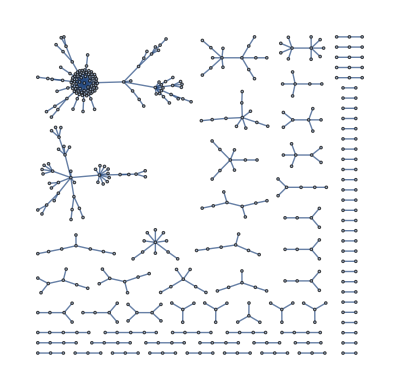

```mathematica
NearestNeighborGraph[Values[wordToVec[[;;,1]]]]  (* NearestNeighborGraph to show the distances between the most frequetly used words *)
```

### Classifying based on distance to pre-defined categories

Patents are categorized based on distance to the vector representations of three nearest words of NBER categories (See Time Series below.).

```mathematica
words=NetExtract[net,"Input"][["Tokens"]];
vecs=NetExtract[net,"Weights"][[1;;-2]];
word2vec=AssociationThread[words -> vecs];
```

```mathematica
nberClassify[wordVector_] :=
Module[ {cat, catToVec, cat2Vec},
cat = {"chemical", "computer", "medical", "electrical", "mechanical"};
catToVec = net /@Nearest[word2vec,word2vec[#],3] &/@{"chemical", "computer", "medical", "electrical", "mechanical"};
cat2vec = AssociationThread[cat -> Flatten[catToVec,{3,1}]];
Return[Nearest[cat2vec,Flatten[wordVector, {2,1}],1]];
]
```

```mathematica
classified = Table[nberClassify[wordToVec[[i]]],{i,100}];
```

```mathematica
Counts[classified]
```

<|{mechanical}→73,{electrical}→13,{chemical}→4,{medical}→9,{computer}→1|>

## Time Series

Instead of the USTPO’s patent classification systems (USPC) which are largely designed for administrative purposes, thus limiting their value for research purposes, the National Bureau of Economic Research (NBER) categories, which Hall, Jaffe, and Trajtenberg (2001) developed by aggregating USPC classes into six economically relevant technology categories (and 37 sub-categories) and classified granted patents accordingly, were applied to create the times series data.

Count the number of patent grant per category per year.

```mathematica
historyStream = OpenRead["historical_masterfile.csv"]
```

InputStream[…]

```mathematica
countPerYear = Association[Table[i->{},{i,17,2017}]];
patentInfoRaw = Read[historyStream, String];
While[patentInfoRaw ≠  "EndOfFile",
patentInfoSplit = StringSplit[StringReplace[Read[historyStream, String],","->" ,"],","][[{3,4,10}]];
pubYear = DateValue[patentInfoSplit[[3]],"Year"];
AppendTo[countPerYear[pubYear],patentInfoSplit[[2]]]
]
```

Plot using the annual dataset from USPTO.

```mathematica
annualStat= SemanticImport["annual.csv"];
```

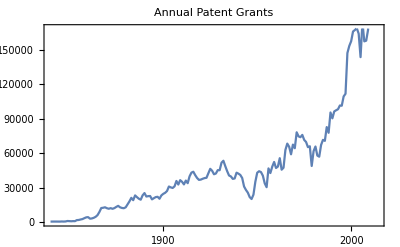
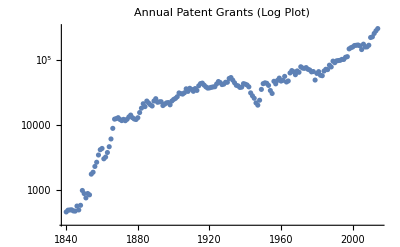

```mathematica
{DateListPlot[TemporalData[Normal[annualStat[;;, "total_iss"]],{"1840","2014"}],PlotLabel->"Annual Patent Grants"], ListLogPlot[TemporalData[Normal[annualStat[;;, "total_iss"]],{1840,2014}],PlotLabel->"Annual Patent Grants (Log Plot)"]}
```

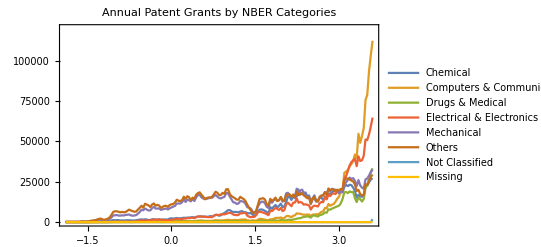

```mathematica
classStat = StringJoin["nber",ToString[#] ,"_iss"]&/@Range[8];
td = TemporalData[Normal[annualStat[;;, #]]&/@classStat,{"1840","2014"}];
DateListPlot[td, PlotLegends->{"Chemical", "Computers & Communications", "Drugs & Medical", "Electrical & Electronics", "Mechanical", "Others", "Not Classified", "Missing"}, PlotRange-> {0,120000}, PlotLabel->"Annual Patent Grants by NBER Categories"]
```

## Scope Checker

We often need to explore the description (or specification) part of patent documents to clarify the scope and details which are claimed in the patent. By constructing the distance matrix between the claim sentence and description sentences, we would be able to find the most similar and related text with a given claim sentence.

Find by the patent number within known file name (“ipgYYMMDD.xml” for known publication date).

```mathematica
patentScopeChecker[files_, patentNum_, claimNum_] :=
	Module[
		{patentsStream,patent, patentTitleRaw, patentTitle, patentText, patentTextRaw, patentSpec, claimsRaw, claims},
		patentsStream = OpenRead[files];
		patent = 
			Find[
				patentsStream,patentNum, RecordSeparators->{{"<?xml version=\"1.0\" encoding=\"UTF-8\"?>"},{"</us-patent-grant>"}}];
		patentTitleRaw = StringCases[patent,Shortest["<invention-title id="~~__~~"</invention-title>"]][[1]];
		patentTitle = StringReplace[patentTitleRaw, Shortest["<"~~__~~">"] -> ""];
		patentSpec = StringReplace[StringCases[patent,Shortest["<description id="~~__~~"</description>"]], "\n" -> " "];
		patentTextRaw=  StringReplace[patentSpec, {Shortest["<"~~__~~">"] -> "",  StringExpression[NumberString,"."] -> ""}];
		patentText = TextSentences[StringJoin[patentTextRaw]];
		claimsRaw = StringReplace[StringCases[patent,Shortest["<claims id="~~__~~"</claims>"]],"\n" -> " "];
		claims =Flatten[TextSentences[StringTrim[StringReplace[claimsRaw, 
		{Shortest["<"~~__~~">"] -> "",  StringExpression[a:NumberString,"."] -> StringExpression[ToExpression[a],":"]}]]]];
		Print["Title: ", patentTitle, "\nClaim: ", claims[[claimNum]], "\nDescription:", Nearest[patentText, claims[[claimNum]],3]];
		PrependTo[patentText, claims[[claimNum]]];
		distanceToText = DistanceMatrix[patentText][[1]];
		Print[distanceToText] //MatrixForm;
		Print[ListLinePlot[distanceToText]];
		Print[NearestNeighborGraph[patentText, VertexLabels->{patentText[[1]] -> "(*
GraphicsBox[TagBox[RasterBox[CompressedData["
1:eJztXU9oXMcZH9pDejBWF1EjOVioslRbYNULuciICIrwoXRz2ZIQQ0TSsG4J
xEmJLOJCyUU1Ti+2Dw6kJhdTiME6+ZKEkBzimw4uOugiWBYjgw++6GQw+LD9
6fu8r7PzZr437715f9b1j5cgS7vvzczvzfdvvvnm1+9/3P7zz5RSa7/A/9p/
+vR3n3zyp7/98Zf4x5sfrX3wl4/Od37/0cXzfzn/yeL7P8cv/4X/buK/g5/7
I4unT5/u7+8/fvz40aNHW1tbm5ubGxsbnU6n1Wo1m82pqakxgtLAv8Gf8AF8
DB/GV/BFfB03wa1wQ9y26p79v+DJkyc7Ozv37t1j7sCIwVce4Fa4IfOLR+BB
eFzVPX4BgYnz3XffXbt27cKFC0tLS6Hok4EH4XF4KB6NBlQ9BiMPTA1Mk9XV
VQxswDmYFng0GoBmoDEvZ2sqPHv2DPoL02FlZaUq+mSgYWgeGommVj1a9QVe
e2grSLa5ubmqGUsGGommosEvZ6sBlqhQUhWK02xAg9HslxI4wq1bt4KrxcNK
nVTqdaWWlWpp1zL98iR9ICBYsaIjVY9lZYDeQffzkDhF1ICjjlKXlfq3Uj8o
tavUQ6X2PK6H9OEf6IuX6SYtuuFUPlrRKXSt6tEtD/DQYUUsLy9nGK7DNOZr
Sl0lFu4r1SNqenR1iaBUV3fwXb7JfbrtVXpEK+sURtfQQXSz6pEuHDAbOp1O
hiE6R+GruzTguzH6MvAok7tLD7pLDz2XiVN0E52teryLwtOnT9fX19OK1mUa
TwzsNg1110YcBv+bmZkgbBrM8rVNDbhJjUkFdBZdfsFChegOJI//IBymcbtM
Y/gwSYRiqG83m6rRuHXmTC80ocacfUhNukzNSyWE0f0Xg9MHDx5cunTJn8cO
zYJtbz14fW5uemIC33339Om9wtg0aN2mRnbScIpBwFBUzUYupArpdEhPbQ/U
VuIF7q6cOjVBVAKLjcZ/Xn21aDajizm9S832BAeRquYkC549e3bt2jVPLXlu
4Fz4GzMYTIhWCNjoJgfeQZHC1jVVd6nx5/wIRSMxLKMVEoRI8TFc2d24S/oo
rVEKARt/VT47erRMKnVOH1JHPJ0aDM6oSN2trS2fRatlTT+mHb2vZ2cXjhyJ
3/Ot2dmfZmZCeStpr0if+pi+GCIMVNVcJQB6wSdmvkbSKZuzD+VopfIA4+Nf
jY2VLGzjLfyBOpgIDFSd1eitW7cSu3CaJNJuDn+/efy4cH8I253x8QrZjLp2
lzqbiBpGd6HWb9y4kdjytUEsLtsogaaPFxfjt+UUIP4ZXGPyZn5VeO4H4ZTj
hD6TFENXH7sIfnEilbOkUKyRHP/rC421CKurq5BX/9PUjcadsbFsT8H4f7uw
cHF+PpSs5v7epO4nElqH8ALaAJNbbuoyiZ08Q+RSl6CSg9v4Ifol5m+GZzGV
mNot8mSDsBnd+a6HaYRhrJZQHyrPkcDJaWdCxr572tRC7XY7asmQyj52LC0d
EZX49huHDgXXvF0ahHP1JjSRyrWsC1XGUF+P2cmYjPpyP2ao/le4MKkCEaAy
MsUXG40i3BwOCSaqUQxpJVTKFuxhik7nHxPcAWOL6abffGVlJe59N5vN6AN/
fe01z+lpUAlAnuM3BTmtXRoWOcJQvpULw0OI2h2mBd9QI/De5KR+czzXum6o
CwrPmC1TefbECf3+0xMTt5vNQkMQV0VC0cEy/VAMJpwCV2NeISsuiFnYo9Wu
KK7OcMkizNboM/hKYsxW15VxNgsNQfRoiF5xE4rhLWele2dnR5dpBg5TO4PY
hGzHvjU7ZN3DE3E1DKpTjyh+8KtfJVJpD1uNj0NNFx1Q2qOBEmYoBhlDXSiV
cHLffvttVwMmSIaEklHbbPxoqySA8Mbyqk30ybMzMy5jRqKyLDb5db1Kg+YC
hrrQqMLGxob74Qf6PWBP75PA0e9/6dIl2YAH1zop1phtjyxeKTzYaHw+OVla
sPeyMKBKYcALonJzc1N47logXcnXHtml+v0heRIXHSCadGEbj9l2iUqr0teN
urB9ka9EtwXDHpxKDJSQM9kJ2v3nXsmwjPV5S+GBrq+v6y+AHrPtUWzQcHYY
Fy5caLVa0T+D+FapCBUWgzHsYRUoRgn9dT2uFSLaY/Tu4vy8/gjMJs8eDXnB
WsyWZ6WVSrwnjx8/1pfXPyStXRqbrFZa8ZZpL1vAnRGCjD1JQciAVHYpndII
ya6urno21fCeojACZqXh6URUPiHoryvs4ZKX1bo0jCfdhIaSt0bQTMfhcK6l
fn0+HC4A/PMuwIsuMzEZd222MSNaijJE9HuTk2UmjPHVS/JZgiTPCxk+wa0F
1piGwbmyspKqwTovioW2jUo9gAY29TRROLl5FknzECpYRCAiJ5VCBO/0IP88
bI/iAfa0YS6fTGzMSv0rcHx05+sPv/lNJflFnFfvyljIGfGDbaCvGxrIuWRp
vbYpW0Z/CuzStDUHIDxlKuNhbYPNsydOVJUtxouhLoCOzBvQBOMnYKBA78jt
WMzQmESecDlTeL2t5oTBJkR9hbl/u2JIIZs5hBnhin0Fd0kiNg2NmTn47Fqt
c0mqOJvfVMem7LCAlAwFUlypPgXZsV2KnRrPgt7P5mfp6ykM16y0sokRq5DN
3ST7Nq28ElRPq5j278UiBhmaHcFYT5GprCGbfAnxhFTReCG6ni2rWb44YrA4
7EdgSDNr/HhGqCyxDTYh4Stnk7OsXfCPxmMMXSuYnUG5gLDX8wjq+PjQs/K5
V0PrKUnpGQab6tixytncpaF2ufogyPNVFxJ+ipiYu7Qq/V4s/pNzm4axTCCr
YCN6ADYzJ+UGvOTp6ZM+JPiYa4W1Ge5A3H7OQ2WfpptOkCy3jcgepEQd2OTL
FR3y8T1dgZSp0NF1/foituAYJG/NEDKCYQ+raSiAWRs2ORrvysGSQ0OmwNFQ
3CLRNmkB/VkwQYNsbzRSmIS+m2zm2P5QxPh86GATZAnqA2+v9VsTVEWniOV4
LidiRMXlRqZCu93WbyuwOaRf6sRmjwbflT4kCByX/bNcTDu7tCXhLNgcRsBs
Uj3vS1iLAZs677Viky9X2oegkqzruYpSy4oI/oBKI8FS5Yj/WAE7Qb+58LGh
ahs1Y7NHFFgByqw9colZVYzGBJXWlcfgSU26tewq8wI2h3b314zNXaLABauw
dW0RCr4Djq+DdczhcIGijKbgGaRGUAiPiL8w5hJD/djccwf6rMn/Q4pDQ3D7
p2dLyWMUka4PpuI2sxFowmeG0jLrxybbQlboOx8Zrv0IE4MqhaEuVpfxjFYu
pBOcyoiseIo+JmMUbjK1TP3Y3CUirGZNfI+Dy5oN7maCSiPtWVGUu4gcYB1Q
l/EYF57LNqHJZm2iB/olOJ6GZetaNLkZOrvy69nZeKIRqCyhjANMHas2Qd9N
NusRp42P3k0Hm/qSiis2Gzaax3u+4htAMi9iZiPU2tOhpE1VlzWU+AC6onx6
zBbqw5o0ci6o0tymMpXGI9bX10ujkrG/v59Yk7MO65vWy1U8QbcBjKXACGvh
JmbPFlqH3KukBPqTJ0/kig01yT2IX133kkrkDrhMoFAhIKuMxYhVWCjb2Oxp
oNosL3lSuIJCbAi5dgzNhlOaPdrZYdy/uJ2J/oQ61+XHxyFJKufOOi/uOmpJ
8c4jIyEqwnIgpcl2rBEBhotUh9JVfVrPtddwaDRAaJk7xTyv+44IPEjk8yut
r2eogB4czLenp42b16r2IwS+PXOYCEX7ayVyhRAfqIynnjI6gdg8MH6Gg3hw
B+pTJJABg9BasRyu8d/n52tF6J479QtUugzayyFMoO1Y7QKVO32rIGAoXAU6
4FjVh9Cee18DqHTltOcPtse3SCtS1rU9xMdIDNMx9dvflr+j0zWqrvA7qDR2
O0bImWzJmXjTw8YPbKH6H9/jCnIuHDkCc64OpYxdaZmg0iVe8r9Cca9kdXW1
JqasAPZcrLtW8XJCje6WW+PCelkBKl3nleTJabfWLlDFFEspCK5op6LdndWq
0YcONkGla5NCHoMWnY1PTDyoaorSAQa/GY0fgOtkVuWN7jnYbMZqEjKmcrCJ
l/bO2FjclK22HD0XHkn7LSFED6l75dSpSibpnmMlBVRaFcTpfHMzvh6tApXU
yICdnZ0OAVobFjXYge3n7yXhHRACgFy9pOQzO/YctRFcFSpez8omB9jjOT9C
ZrIVjwjpqbPAWlMlOpvY8x0D+3ZCB7ZuzgMI0rL5uqs1NixnZbNnW8QEPCtx
YSJg3Hgq5ePwf5B76n82sRBewCT97OjR0ibpXsqTQLOxyT5mfH83qEkcLvgF
cEXZ+Q247umKdBkATfhkYrwRrRLW0d6anYUlXwKh5bBp9TGVh/2D1x48suEE
ARiwSKArNhIHnu6z/0U+GRZS9/rcXNGmUVo2M+hNl48pVyKNrxqH9UlxN9g8
eATkA1qSeIIkzEKf7Wn4jHCu6Jt4IYsMGQl6M6BNG6+Ppygw6xoTCDejsE/R
aUJ4r8CsKw8cBKG1kCQ+Szwwn6QDRo8d4zBgEZNUsGmD+JvC0XtWMctVJgyf
FP8sJ00I1jLmbDS5QC4aA/mZQcLjW67wC8b24vx8EaaR4G+GigV9HdvtxT2y
ugBWdYZ5UWYUF9ISUxUM5nSF2J+1jiE8tcVG43azGbb0hxALChWntUY141sk
MCtd0ZUxAtqDiVPbVTMXIIKcp4o0GhdpyTsUm0KcNv8aSs8xMZUtY0QuDq9j
Y2MDr33AvZxFA60VikyePXECo7QbKMhgBajMv77ZoxKg1psYXGBigk2fc5AZ
UASYyPVfEo3AYUDn2RzHjn2eOxIor2/mzD1gx8S6dwkvatw4RH+hp/Aa47me
tLInWAk72SBFjejN/3ZhIfNheXLuQc68IFfEQPkl5nF0BbS6Nukz6plKJEMw
dxUtTGTzX+S8oDw5exzKW7Ttq/U/JYER9z0ZNT+qWwa/qy7B2zx+/M7YWFpO
5Zy9PPm0aMZXcJ9tbKbN5jIOpmFgwo5QuoILECwuMx4dTOuTyvm0eXLdrZnP
jFRr065Vfpi1dcu8zQZeG7JnMgx80j0/TSrnumfeh8I5BtaJmXbHkPXVhSFR
3PBWBacL02i8Qwc9JApDeR9KP+seMdz5HYeb2W63/cWs1QwrLcpXMoQyPopm
wfW5OWEGJe4R62fdv4kpHy8Rw0jlUFjl/OhaPomQz0m8SBmewgxK3L+ZYW81
XpIrp065muRvulhDQ4knM440YO+5xg2uqHyqjs/e6mx1D6yOiaJwq2c4zmr8
hF2triGgg6yGCm8BllWbT92DfsqaJByYdZ0IALfRs1/WiVlc1aD6wNrxL6am
ZD/FsyZJP2W9oK47/uNPB17ReIjYWuEZn4RfvEPYIvDP+OXILbX0KRclnlzE
oSHZoPWvF+Rfy0uI/zA8CwXjY/FoHvjF7/Hqor8QR3BSYB6vrKxA/DYJcwT+
Gb/En/ABTpTF+3njxg18F3TX2R6OpxXxBrREZ9O/llffu86eEP9R5Fl4Kk3/
pbE8gBKH5Afd4BovMEcyHxP2CWhtmRZX3ATCK+1TXyJVnb2+dw1MIf6jaHL5
RG/ks+nLAV5p2GCdToeJxpS5R2BJzqSHJTp+mBdeNjiYPvtZ0tbA9KlPy2aV
y81U3n5i4jF8FQLiBTIcRGNGw1fCWEGAg24IE/QOXIPobFta4qasj7qMlKYL
rkyYxNrRXTqoXRgKT+fCtXBTZ4zRVinW2tDXoBvihac2J4nJ+jq+jgyXxHMB
JUPt6H5SXXd+rvUgbwYEuGfGlHCADqcRGqZOi9B2AH+KLCV8UV4qLQeGvo5T
iUamOn43Q113+cyFPT4fwQ3/JQ8Os0eaKy7QoL9YeaFJiWIND8Vn2IvBF6OM
aMYGAY+QQ2plAlTebjb9E3Wynbkgn4eCpwv2j0oT0GPPMfIZS1j24kf4b2Qo
EOPjV06d8t/Jm/k8lL77rKJZckxcRyqrquvmecLq5Op49/TpN0liCwolJ2D5
+FOZ56yivniOGLS2sI8j1SpYhZDPKJ+jPUEPKWd1jxL4v11YuHXmzD+XlsDC
O7Ozbxw6tEwx6oUjR6YnDuByvS2gRcy0aed5zhHru00UeUtO+ZVms8E8ZCoG
TE/dPumS5uJrjy7Q/dPMDFiG7rtOK5KfT06uUbQTmuit2dmzJ07gzcf1PHJF
P+P3f5+fT1UqIf8Zf33x/E2B0GrLGqQCVLYzL53ABQ3kcdZZZvcNX8FrAKJx
fRO78MtUU3I30PmbffeSisBmkHPcSkOCOdRofJW1rnvXfaW9T5CzcftirMZK
qODD1hYSm+p5afeSy1MYV6hzq/vuM+WthEIjFzTmxSEx7A+V91NFFaTDninf
t4WIBTZHSGlGgKcmm0OK0thSRWyCXF1a/HJNTJCSbYui/6JVqGowJQMOsmwO
KYpLl1+zy7U3QeWoJCD4nrzXkn/2X9OsIeTDFw5ANd5Lm549XqVywNPHdAG+
tsuOjX5f8p7osDDParSCihiUYBF1KY7nCrhhwPMnpgrKhcvPjvpWETk6xID7
X4JF1HNHfhSVXcrf2f39fdf9Wd6O4nY8A0K5mAhvHDpUaCEg2Y5V4QoVCuaQ
NcVo5PDgwYPEUkKq0XhvcrKgQkAcXT/pfnhAAejaecQo81i3gsAVbxLYVM8X
s4qgUnBJlLZjKBQwAa27ZRlb338f8FmVAE6Wq7awQWhwi6jnjscqyjYvQvoJ
8nbar6BZzeHpX0+nTAJJpFKwfFSRRqaQjAE7/wUgNDE6xFhsNEIRKgQKVMGn
rcl5sPjTiAaFIvgmEw4KOuU8ZOSqO+GHx7PoHBvXHgdGu90e3bgQIzk6NCA0
j0W0l+SPlOYsyOFNaO3RDQ31KTrk434ysllE7Fq+4r4thrfMJCsh4qeo4NtI
61CMZLL7yWg0fkq/DHpVnJVBInhpIWQ4KzrIb3SjClAW/rmaZ2dmUllEl0Uq
VXXLi7KKOagaPbJ+KF7FxMWyCD6FuboezoiqdDOydWOpDryEd778sqrm5YRX
dGiAz44elal0lSwwqKzW5EgkFPjHpUt13h4rQLDeTTQaLouIlywT6+pXTiUD
bUh8jd9vt0dR6noewPEc4+NGYlh3UKzAXlZJAwawDlQyfKLWzePHfxy1lVDh
fFUrzlLebG8wJe97KEqmsoYF6GQrl/Hp+fOj5bxYyzkK4JPFdkm6Ctt2ItQ5
QQ6OkrNy8gDwmn8cqcrtPm+pDlhEPlNyJIq1bm1t+bzMmKSjoknhfvpHhw7g
riQQAUM0KjkbkKU+ixHQpOB0JCapcMafDj2VUQAGZ7TUDR8p5dM1+KRfXLlS
fxdGyL6IqPShG8NSQ5vHB9ALnjJq4ciRO19+Wec39tGjRyncTxswFPVXlDJA
kL+R/+bSEjitbYA3rTmkA4NQ53fVH/Iph3FAn0Kz1NBGirau+K6wDIDu1yc4
EATozvr6eqpxmJ6YgEr1KUtSQuNhreEF88oEGwCdRZdfMB513Lt3zzP3Rsf7
7faPVA6x5EwV2GYQ+5hZ/0gTEWKgm/Uv65EfeMkxPkI+pwuHiVbYhJubmxjk
gt55GJy4ORcdggOVGAyJA11DB0fC8woFvPYwKtIqIMYrtHjabrfhNYBcCMCc
Dg6mPG4C+nBD3NbnFF0r/M80f1GB7i8tLWUbPQNTU1PwAiDioG1hGx8I5++/
5zJTBz/QhV/iT/gAPoZJFKSMGxqPLtQ54lomYORAsmFeBOG0TKDBaDYaX7md
VjdgQGA2CAdv1QpoJJqKBr/kUQCMEOgd/yBS+eCQDho5ogG6qsASeHV1NZRi
zQZWi2jGS4kaBLA5MR24dH+qteM8wIPYZsajR31HRj2BqREVod3Y2Gi1WgHn
LG6FG+K2uDkXyH05E0sDR9ugvw68xa0t5hd+BxiBwwhvJb7ayL/Bn/QS/ZuD
KBMfxDDSgbj/AknU3b8=
"], {{0, 153}, {154, 0}}, {0, 255},
ColorFunction->RGBColor],
BoxForm`ImageTag["Byte", ColorSpace -> "RGB", Interleaving -> True],
Selectable->False],
DefaultBaseStyle->"ImageGraphics",
ImageSize->{23.5, Automatic},
ImageSizeRaw->{154, 153},
PlotRange->{{0, 154}, {0, 153}}])\nClaim"}]];
		Close[patentsStream];
	]
```

Title: Method and system for presenting input expressions and evaluations of the input expressions on a workspace of a computational system
Claim: 2: The method according to claim 1, wherein the first user interface mechanism and the second user interface mechanism are different user interface mechanisms.
Description:{For example, the first GUI mechanism and the second GUI mechanism could be different states of a single GUI mechanism.,If a pull-down menu is utilized, the first GUI mechanism may be activated by selecting an appropriate item in the menu.,For instance, the second GUI mechanism may be presented in response to activation of the first GUI mechanism.}

{0,173,141,108,122,125,165,126,119,117,141,123,136,253,146,123,116,120,127,122,121,1528,212,119,120,203,221,180,153,112,192,227,185,109,203,172,135,117,245,214,179,129,118,136,115,177,128,213,261,124,121,129,126,114,119,123,118,119,173,118,116,120,148,121,116,126,243,122,163,132,157,125,153,129,165,122,119,120,123,137,119,122,111,122,145,119,121,116,244,117,131,128,118,117,144,125,126,119,116,120,301,127,112,123,133,119,192,117,122,127,116,130,135,121,117,142,134,126,119,196,123,121,117,168,120,112,135,123,123,117,117,123,117,115,116,111,147,122,133,190,266,118,150,123,142,116,104,121,120,122,128,147,108,118,127,126,147,122,113,128,157,118,112,147,135,115,106,147,116,108,193,251,124,152,121,140,116,107,121,120,119,132,132,113,116,132,130,121,124,126,112,134,158,147,111,118,139,91,352,222,180,198,123,226,120,119,144,116,127,120,116,118,118,124,139,122,160,116,111,121,133,119,193,115,121,133,119,191,121,122,127,116,120,127,115,127,116,121,117,119,135,121,119,194,123,118,119,135,121,119,192,127,308,120,125,154,117,114,128,128,122,118,119,120,115,136,151,173,125,201,119,120,116,118,183,112,171,148,156,139,139,126,153,216,265,285,120,142,159}

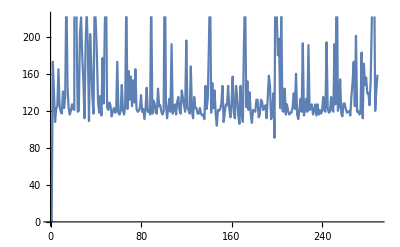

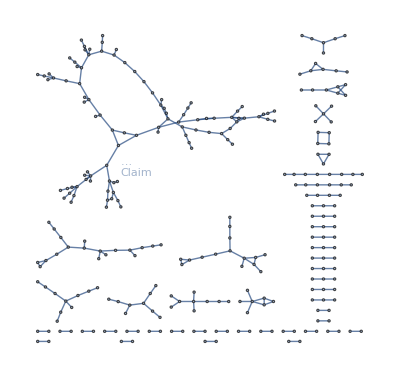

```mathematica
patentScopeChecker["ipg130326.xml","08407580",2]
```

Title: Power converter
Claim: 4: The power converter of claim 1, wherein the air intake direction is substantially perpendicular to the air discharge direction.
Description:
{The direction opposite to the front direction will be defined as a rear direction.,The direction horizontally intersecting the front-rear direction will be defined as a left-right direction.,The direction vertically intersecting the front-rear direction will be defined as an up-down direction.}

{0,198,125,398,209,240,830,161,146,101,104,100,103,104,266,101,90,126,191,124,103,101,93,94,121,102,128,97,76,77,77,114,110,371,87,388,103,232,104,92,95,93,115,103,95,98,108,97,167,148,138,107,137,167,108,117,97,117,98,99,94,98,91,96,96,92,98,112,96,108,93,99,106,149,102,128,111,97,124,124,95,177,96,94,148,99,198,116,115,85,85,392,97,182,147,92,95,212,216,165,263,94,102,91,97,87,126,131,114,177,108,123,134,130,109,96,198,130,97,108,89,97,120,313,127,93,150,90,160,97,132,194,268,110,125,116,126,135,126,105,91,167,99,103,186,166,139,175,260,93,92,185,181,95,137,93,109,97,203,130}

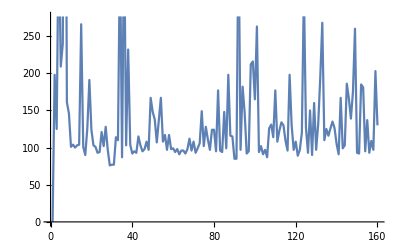

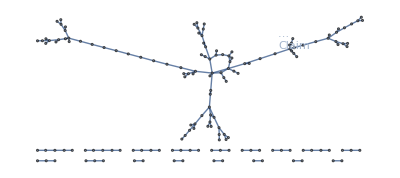

```mathematica
patentScopeChecker["ipg160105.xml","09232684",4]
```